## Hexi—PS9—2025-02-21

### Exercises from EIWL3 Section 23

```mathematica
N[Sqrt[2],500]
```

1.4142135623730950488016887242096980785696718753769480731766797379907324784621070388503875343276415727350138462309122970249248360558507372126441214970999358314132226659275055927557999505011527820605714701095599716059702745345968620147285174186408891986095523292304843087143214508397626036279952514079896872533965463318088296406206152583523950547457502877599617298355752203375318570113543746034084988471603868999706990048150305440277903164542478230684929369186215805784631115966687130130156185689872372

```mathematica
Table[RandomReal[1],10]
```

{0.156147,0.856513,0.990291,0.85683,0.449148,0.91963,0.557978,0.208797,0.399471,0.231085}

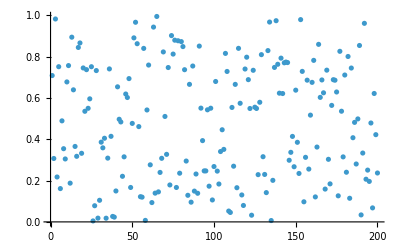

```mathematica
ListPlot[Table[RandomReal[1],200]]
```

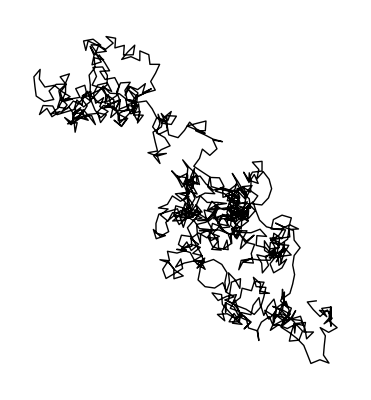

```mathematica
Graphics[Line[AnglePath[RandomReal[{0,2Pi},1000]]]]
```

```mathematica
Table[Mod[n^2,10],{n,0,30}]
```

{0,1,4,9,6,5,6,9,4,1,0,1,4,9,6,5,6,9,4,1,0,1,4,9,6,5,6,9,4,1,0}

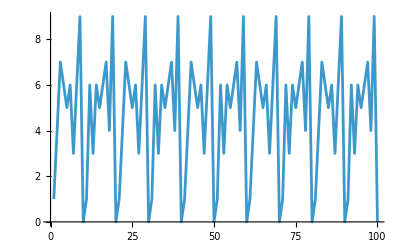

```mathematica
ListLinePlot[Table[Mod[n^n,10],{n,1,100}]]
```

```mathematica
Table[Round[Pi^n],{n,10}]
```

{3,10,31,97,306,961,3020,9489,29809,93648}

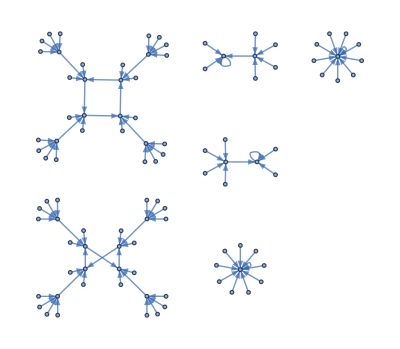

```mathematica
Graph[Flatten[Table[n->Mod[n^2,100],{n,0,99}]]]
```

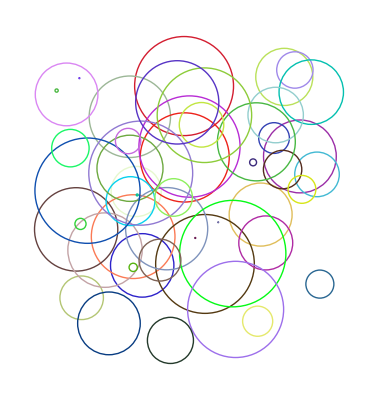

```mathematica
Graphics[Table[Style[Circle[{RandomReal[10],RandomReal[10]},RandomReal[2]],RandomColor[]],50]]
```

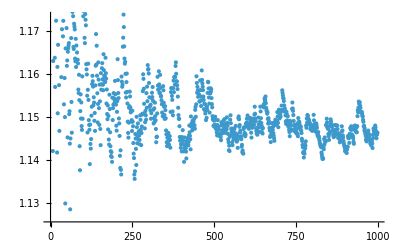

```mathematica
ListPlot[Table[Prime[n]/(n Log[n]),{n,2,1000}]]
```

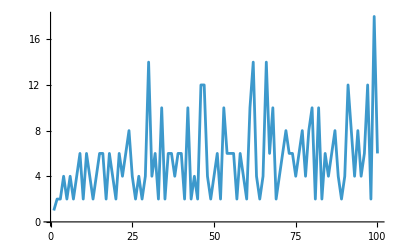

```mathematica
ListLinePlot[Table[Prime[n+1]-Prime[n],{n,100
}]]
```

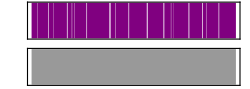

```mathematica
Sound[Table[SoundNote["C",RandomReal[0.5]],20]]
```

```mathematica
ArrayPlot[Table[Mod[i,j],{i,50},{j,50}]]
```

-Graphics-

```mathematica
Table[ArrayPlot[Table[Mod[x^y,n],{x,50},{y,50}]],{n,2,10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Exercises from EIWL3 Section 24

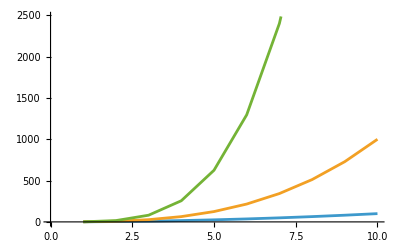

```mathematica
ListLinePlot[{Table[x^2,{x,10}],Table[x^3,{x,10}],Table[x^4,{x,10}]}]
```

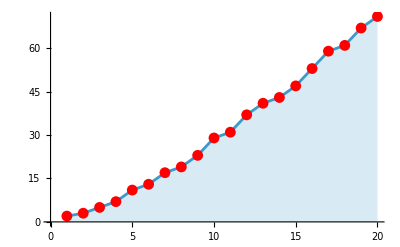

-Graphics-

```mathematica
ListLinePlot[Table[Prime[x],{x,20}],Filling->Axis,Mesh->All,MeshStyle->Red]
```

```mathematica
ListPlot3D[GeoElevationData[GeoDisk[Entity["Mountain","FujiSan"],20 Quantity[, "Miles"]]]]
```

-Graphics3D-

```mathematica
ReliefPlot[GeoElevationData[GeoDisk[Entity["Mountain","FujiSan"],100 Quantity[, "Miles"]]]]
```

-Graphics-

```mathematica
ListPlot3D[Table[Mod[i,j],{i,100},
{j,100}]]
```

-Graphics3D-

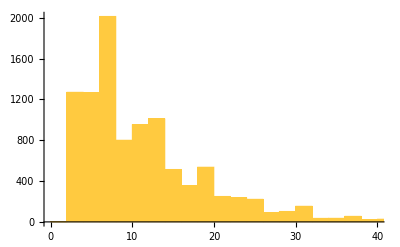

```mathematica
Histogram[Table[Prime[n+1]-Prime[n],{n,10000}]]
```

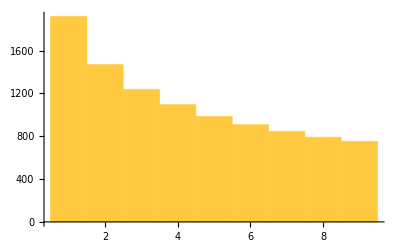

```mathematica
Histogram[Table[Part[IntegerDigits[n^2],1],{n,10000}]]
```

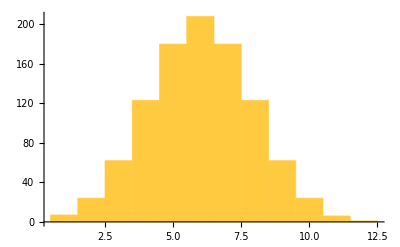

```mathematica
Histogram[Table[StringLength[RomanNumeral[n]],{n,1000}]]
```

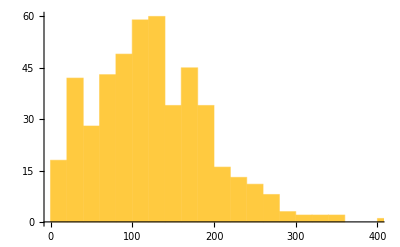

```mathematica
Histogram[StringLength[TextSentences[WikipediaData["computers"]]]]
```

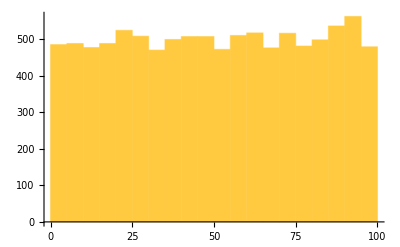
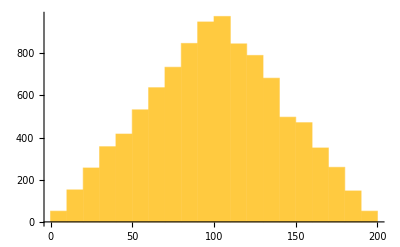
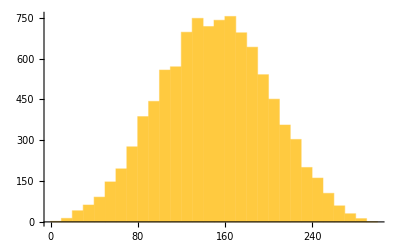
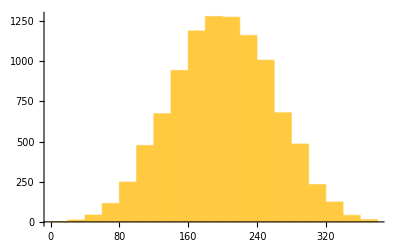
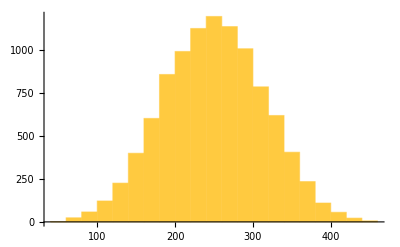

```mathematica
Table[Histogram[Table[Total[RandomReal[100,n]],10000]],{n,1,5}]
```

```mathematica
ListPlot3D[ImageData[Binarize[Graphics[Style[Text["W"],200]]]]]
```

-Graphics3D-

### Exercises from EIWL3 Section 25

```mathematica
f/@Range[5]
```

{f[1],f[2],f[3],f[4],f[5]}

```mathematica
f/@g/@Range[10]
```

{f[g[1]],f[g[2]],f[g[3]],f[g[4]],f[g[5]],f[g[6]],f[g[7]],f[g[8]],f[g[9]],f[g[10]]}

```mathematica
x//d//c//b//a
```

a[b[c[d[x]]]]

```mathematica
Alphabet[]//Framed
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

```mathematica
EntityValue[EntityClass["Planet",All],"Image"]//ColorNegate
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
GeoGraphics/@EntityList[EntityClass["Country","GroupOf5"]]
```

GeoServer::vtiles: Unable to download one or more vector tiles.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ImageCollage[Binarize/@EntityClass["Country","Europe"][EntityProperty["Country","Flag"]]]
```

-Graphics-

```mathematica
Column[Map[DominantColors,EntityClass["Planet",All][EntityProperty["Planet","Image"]]]]
```

{GrayLevel[0.0003583302785574673],GrayLevel[0.37819453023602134],GrayLevel[0.6046533866694355]}
{RGBColor[0.8853258461241997, 0.6847278045450479, 0.4256700402289714],RGBColor[0.000642062052308579, 0.001403728557887932, 0.0007410746962000475]}
{RGBColor[0.0024606903915941458, 0.002409786977322984, 0.003967391669501376],RGBColor[0.38137481479305974, 0.40751891927937794, 0.4878718697498957],RGBColor[0.7093695751573504, 0.7271479152421573, 0.8068003834919311],RGBColor[0.9792341072655132, 0.9822919456302736, 0.9938424502332899],RGBColor[0.6354966433925654, 0.5479933929894801, 0.5436090390913342]}
{RGBColor[0.0012177093066651906, 0.0015444381797393631, 0.002282631159508306],RGBColor[0.5556976435501926, 0.4531266000126358, 0.33304542075624793],RGBColor[0.97661432353462, 0.6748004218195973, 0.3694536477636728],RGBColor[0.247985366921424, 0.2813954280094231, 0.26899240204489205],RGBColor[0.4966218764141378, 0.5143298636117646, 0.5023898418540108],RGBColor[0.6400489241717509, 0.7400325150547418, 0.8829327228050379]}
{RGBColor[0.0007307420384636347, 0.0007454959245913933, 0.0016562167031508943],RGBColor[0.678269963164705, 0.6320729858749744, 0.5998391342654895],RGBColor[0.8542680892787012, 0.7080302078893711, 0.5495188294199109],RGBColor[0.5603508711436291, 0.4463794016412469, 0.3598178300902997]}
{RGBColor[0.0008759669414015513, 0.0006167590991106197, 0.001366050596437346],RGBColor[0.3645501167535891, 0.34744090241667425, 0.30085819908851064],RGBColor[0.6925169040198021, 0.6087670195382209, 0.4578034718491758],RGBColor[0.9019996055101402, 0.7638467064934565, 0.49272539097128865]}
{RGBColor[0.5487856307291583, 0.6154747806199766, 0.6457820783876971],RGBColor[0.0026251717182227572, 0.0020772457357266776, 0.0024667841667845715],RGBColor[0.22748358078321199, 0.24605669677627076, 0.25518636693604435]}
{RGBColor[0.6462468675595785, 0.7691692304223126, 0.8252791002211531],RGBColor[0.00014484531684443174, 0.00019326545709415257, 0.0002527639647539288],RGBColor[0.42841487713890164, 0.5053577956882549, 0.5435623692316727]}

```mathematica
Total[LetterNumber["wolfram"]]
```

88